```mathematica
shellVolExact[R_,dR_]:=4*Pi*(R^2*dR+R*dR^2+(dR^3)/3)
shellVolApprox[R_,dR_]:=4*Pi*(R^2*dR)
```

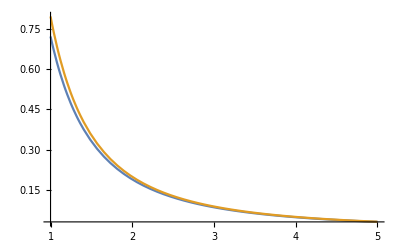

```mathematica
Plot[{1/shellVolExact[R,0.1],1/shellVolApprox[R,0.1]},{R,1,5},PlotRange->All]
```

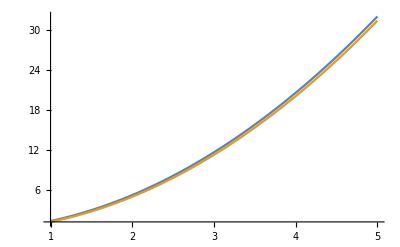

```mathematica
Plot[{shellVolExact[R,0.1],shellVolApprox[R,0.1]},{R,1,5},PlotRange->All]
```

```mathematica
Plot[{1/shellVolExact[R,0.1],1/shellVolApprox[R,0.1]},{R,1,5},PlotRange->All]
```

-Graphics-